# Degradability conditions

```mathematica
AddAssumption[assumption_]:=$Assumptions=DeleteDuplicates[$Assumptions&&assumption];
Needs["QuantumUtils`"]
```

AssignUsage::nousg: No usage message in UsageData[] for symbol PossiblyTrueQ found; using a blank message instead.

AssignUsage::nousg: No usage message in UsageData[] for symbol PossiblyFalseQ found; using a blank message instead.

AssignUsage::nousg: No usage message in UsageData[] for symbol PossiblyNonzeroQ found; using a blank message instead.

General::stop: Further output of AssignUsage::nousg will be suppressed during this calculation.

## Setting

### Dimension

Set the dimension of the Hilbert Space

```mathematica
d=4;
```

### Input state

Use this function to generate a d-dimensional generic density matrix

```mathematica
BuildDensity[par_]:=(
protected=Unprotect[Conjugate];
ρSys = ConstantArray[0,{d,d}];
Do[
ρSys[[i1,j1]]=ToExpression[ToString[par]<>ToString[i1-1]<>ToString[j1-1]];
ρSys[[j1,i1]]=Conjugate[ToExpression[ToString[par]<>ToString[i1-1]<>ToString[j1-1]]],
{j1,1,d},{i1,1,j1-1}
];
Do[
Conjugate[ToExpression[ToString[par]<>ToString[j1-1]<>ToString[j1-1]]]=ToExpression[ToString[par]<>ToString[j1-1]<>ToString[j1-1]];
ρSys[[j1,j1]]=ToExpression[ToString[par]<>ToString[j1-1]<>ToString[j1-1]],
{j1,1,d}
];
Protect[Evaluate[protected]];
ρSys
)
```

### Transition matrices

This function generates the matrix of transition probabilities, whose (ji) element is (par)ji. MAD channels are in a one-to-one relationship to these transition matrices.

```mathematica
GammaMat[par_]:= (
protected=Unprotect[Conjugate];
gam =IdentityMatrix[d];
Do[
Do[
gam[[j,i]]=ToExpression[ToString[par]<>ToString[j-1]<>ToString[i-1]];
Conjugate[ToExpression[ToString[par]<>ToString[j-1]<>ToString[i-1]]]=ToExpression[ToString[par]<>ToString[j-1]<>ToString[i-1]];
Conjugate[Sqrt[ToExpression[ToString[par]<>ToString[j-1]<>ToString[i-1]]]]=Sqrt[ToExpression[ToString[par]<>ToString[j-1]<>ToString[i-1]]],
{i,1,j-1}
];
gam[[j,j]] =1- Sum[ToExpression[ToString[par]<>ToString[j-1]<>ToString[i-1]],{i,j-1}];
Conjugate[1- Sum[ToExpression[ToString[par]<>ToString[j-1]<>ToString[i-1]],{i,j-1}]]=1- Sum[ToExpression[ToString[par]<>ToString[j-1]<>ToString[i-1]],{i,j-1}];
Conjugate[Sqrt[1- Sum[ToExpression[ToString[par]<>ToString[j-1]<>ToString[i-1]],{i,j-1}]]]=Sqrt[1- Sum[ToExpression[ToString[par]<>ToString[j-1]<>ToString[i-1]],{i,j-1}]],
{j,1,d}
];
Protect[Evaluate[protected]];
gam
);
```

Build transition matrix - single transition

```mathematica
GammaMatADC[par_,levup_,levdown_]:= (
protected=Unprotect[Conjugate];
gam =IdentityMatrix[d];
gam[[levup+1,levdown+1]]=ToExpression[ToString[par]<>ToString[levup]<>ToString[levdown]];
Conjugate[ToExpression[ToString[par]<>ToString[levup]<>ToString[levdown]]]=ToExpression[ToString[par]<>ToString[levup]<>ToString[levdown]];
Conjugate[Sqrt[ToExpression[ToString[par]<>ToString[levup]<>ToString[levdown]]]]=Sqrt[ToExpression[ToString[par]<>ToString[levup]<>ToString[levdown]]];
gam[[levup+1,levup+1]]=1-ToExpression[ToString[par]<>ToString[levup]<>ToString[levdown]];
Conjugate[1-ToExpression[ToString[par]<>ToString[levup]<>ToString[levdown]]]=1-ToExpression[ToString[par]<>ToString[levup]<>ToString[levdown]];
Conjugate[Sqrt[1-ToExpression[ToString[par]<>ToString[levup]<>ToString[levdown]]]]=Sqrt[1-ToExpression[ToString[par]<>ToString[levup]<>ToString[levdown]]];
Protect[Evaluate[protected]];
gam
);
```

Function to clear amplitudes parametrized by par

```mathematica
ClearAmplitudes[par_]:=(
Do[
ToExpression[ToString[par]<>ToString[j]<>ToString[i],InputForm,Clear],
{j,1,d},{i,0,j-1}
]
)
```

## Kraus operators

### Build Kraus operators

Maximum number of Kraus operators

```mathematica
nKmax = d (d-1)/2 +1;
```

ij elements

```mathematica
Krausij[mat_, in1_,in2_]:=(
kr = ConstantArray[0,{d,d}];
kr[[in1,in2]]=Sqrt[mat[[in2,in1]]]; 
Simplify[kr]
);
```

00 element

```mathematica
Kraus00[mat_]:=(
kr= IdentityMatrix[d]; 
Do[
kr[[jj,jj]]=Sqrt[mat[[jj,jj]]],
{jj,1,d}
];
Simplify[kr]
);
```

List of Kraus operators

```mathematica
KrausList1[mat_,in_]:=If[in==0,
Kraus00[mat],
(jj=1+Floor[(1+Sqrt[1+8*(in-1)])/(2)];
ii=in-((jj-1)*(jj-2)/2);
Krausij[mat,ii,jj]
)
];

KrausList[mat_]:=(
KrausListTMP={};
Do[
If[KrausList1[mat,lkj]===ConstantArray[0,{d,d}],
0,
AppendTo[KrausListTMP,KrausList1[mat,lkj]];
],
{lkj,0,nKmax-1}
];
Simplify[KrausListTMP]
)
```

Number of non-zero Kraus operators

```mathematica
nK[mat_]:=Length[KrausList[mat]];
```

## MAD channel

```mathematica
MAD[par_]:=Kraus[KrausList[GammaMat[par]]]
```

## Complementary channel

```mathematica
KrausTrace[θ_,M1_,M2_] := Simplify[Tr[M1.θ.ConjugateTranspose[M2]]];
ComplMAD[θ_,mat_]:=(
dimEnv = nK[mat];
krausset=KrausList[mat];
th =ConstantArray[0,{dimEnv,dimEnv}];
Do[
th[[i,j]]=KrausTrace[θ,Part[krausset,i],Part[krausset,j]],
{i,1,dimEnv},{j,1,dimEnv}
];
Simplify[th]
)
```

## Erasure channel

```mathematica
LevelErasure[den_,level_,mat_]:=(
den1=den;
Do[
den1[[i,i]]=den[[i,i]]+mat[[level+1,i]]*den[[level+1,level+1]],
{i,1,d-1}
];
Do[
den1[[i,level+1]]=0;
den1[[level+1,i]]=0,
{i,1,d}
];
Simplify[den1]
)
```

## Inverse channel

### Modified amplitudes

We can write the inverse for a generic MAD channel as a composition of inverse ADC’s whose amplitudes can be derived from the original channel, as seen in inverse.tex

```mathematica
ModifiedAmplitudes[mat_]:=(
modamp=ConstantArray[0,{d,d}];
Do[
Do[
sum =0;
Do[
sum = sum + Part[mat,i,k],
{k,j+1,i-1}
];
Part[modamp,i,j]= Part[mat,i,j]/(1-sum),
{j,1,d}
],
{i,1,d}
];
modamp//Simplify
);
```

### Pseudo Kraus operator

The inverse of an ADC can be written in a pseudo-Kraus representation. Here we store the pseudo-Kraus operators in a list

```mathematica
InverseNotKraus[mat_]:=(
invk=ConstantArray[0,{d,d}];

Do[
invk[[i,j]]={},
{j,1,d},{i,1,d}
];

moda=ModifiedAmplitudes[mat];

Do[
K0inv  = IdentityMatrix[d];
K0inv[[j,j]]= 1/Sqrt[1-moda[[j,i]]];
K1inv = ConstantArray[0,{d,d}];
K1inv[[i,j]]=Sqrt[moda[[j,i]]/(1-moda[[j,i]])];
AppendTo[Part[invk,j,i],K0inv];
AppendTo[Part[invk,j,i],K1inv],
{j,2,d},{i,1,j-1}
];

invk//Simplify
);
```

### Inverse map of an ADC

This function returns the output of the inverse of an ADC

```mathematica
InverseADC[θ_,mat_,j_,i_]:=Part[InverseNotKraus[mat],j,i,1].θ.Part[InverseNotKraus[mat],j,i,1] - Part[InverseNotKraus[mat],j,i,2].θ.Transpose[Part[InverseNotKraus[mat],j,i,2]]//Simplify;
```

### Inverse of a MAD channel

```mathematica
InverseMAD[θ_,mat_]:=(
θ1=θ;
Do[
θ1=InverseADC[θ1,mat,d+1-jjj,iii],
{jjj,1,d},{iii,1,d-jjj}
];
θ1//Simplify
);
```

## Choi matrix

### Choi matrix for a generic MAD channel

Convert channel into Choi matrix

```mathematica
Choigen=Choi[MAD4gen];
Simplify[Eigenvalues[Choigen]]
```

{0,0,0,0,0,0,0,0,0,γ10,γ20,γ21,γ30,γ31,4-γ10-γ20-γ21-γ30-γ31-γ32,γ32}

Write Choi matrix from scratch

```mathematica
ChoiMatrix[ch_]:=(

dimOut=OutputDim[ch];
choi=ConstantArray[0,{d*dimOut,d*dimOut}];
dm=ConstantArray[0,{d,d}];

Do[
dm[[i,j]]=1;
dmprime=ch[dm];
dm[[i,j]]=0;
Do[
choi[[(i-1)*dimOut+i1,(j-1)*dimOut+j1]]=dmprime[[i1,j1]],
{j1,1,dimOut},{i1,1,dimOut}
],
{i,1,d},{j,1,d}
];

choi
)
```

### Choi matrix for inverse map

```mathematica
ChoiMatrixInv[mat_]:=(
CMinv=ConstantArray[0,{d*d,d*d}];
dm=ConstantArray[0,{d,d}];

Do[
dm[[ik,jk]]=1;
dmInv=InverseMAD[dm,mat];
dm[[ik,jk]]=0;
Do[iik=1,iik<=d,iik++,
CMinv[[(ik-1)*d+iik,(jk-1)*d+jjk]]=dmInv[[iik,jjk]],
{iik,1,d},{jjk,1,d}
],
{ik,1,d},{jk,1,d}
];

CMinv
);
```

### Choi matrix for complementary channel

```mathematica
ChoiMatrixCompl[mat_]:=(
nkr=nK[mat];
CMcompl=ConstantArray[0,{d*nkr,d*nkr}];
dm=ConstantArray[0,{d,d}];

Do[
dm[[ik,jk]]=1;
dmEnv=ComplMAD[dm,mat];
dm[[ik,jk]]=0;
Do[
CMcompl[[(ik-1)*nkr+iik,(jk-1)*nkr+jjk]]=dmEnv[[iik,jjk]],
{iik,1,nkr},{jjk,1,nkr}
],
{ik,1,d},{jk,1,d}
];

CMcompl
)
```

### Choi matrix for connecting map

```mathematica
ChoiMatrixConnecting[mat_]:=(
nkr=nK[mat];
CM1=ConstantArray[0,{d*nkr,d*nkr}];
dm=ConstantArray[0,{d,d}];

Do[
dm[[ik,jk]]=1;
dm1=InverseMAD[dm,mat];
dm2=ComplMAD[dm1,mat];
dm[[ik,jk]]=0;
Do[
CM1[[(ik-1)*nkr+iik,(jk-1)*nkr+jjk]]=FullSimplify[dm2[[iik,jjk]]],
{iik,1,nkr},{jjk,1,nkr}
],
{ik,1,d},{jk,1,d}
];

CM1//Simplify
);
```

## Check eigenvalues function

Mathematica seems janky when it comes to finding eigenvalues, a function that checks whether a set of values is the set of eigenvalues for a matrix seems necessary

```mathematica
CheckEigenvalues[mat_,eigenvals_]:=(
dim=Dimensions[mat][[1]];
dim1=Dimensions[eigenvals][[1]];
id=IdentityMatrix[dim];
bool=True;
Do[
bool=bool&&Simplify[Det[mat-eigenvals[[i]]*id]==0],
{i,1,dim1}
];
Simplify[bool]
)
```

## Degradability conditions

### (1) MAD3

MAD3 channel embedded into H4

#### (a) Single decay

```mathematica
Γ1a= GammaMat[γ1a];
γ1a30=0;
γ1a31=0;
γ1a32=0;
γ1a20=0;
γ1a21=0;
Choi1aConn=ChoiMatrixConnecting[Γ1a];
```

```mathematica
ei1a=Simplify[Eigenvalues[Choi1aConn]]
Reduce[CheckEigenvalues[Choi1aConn,ei1a],γ1a10]
```

{0,0,0,0,1/(1-γ1a10),1,1,(-1+2 γ1a10)/(-1+γ1a10)}

True

#### (b) γ_(2,1)=0, γ_(3,i)=0 ∀i

```mathematica
Γ1b= GammaMat[γ1b];
γ1b30=0;
γ1b31=0;
γ1b32=0;
γ1b21=0;
Choi1bConn=ChoiMatrixConnecting[Γ1b];
```

```mathematica
ei1b=Simplify[Eigenvalues[Choi1bConn]]
Reduce[CheckEigenvalues[Choi1bConn,ei1b],{γ1b10,γ1b20}]
```

{0,0,0,0,0,0,0,0,1,(-1+2 γ1b10)/(-1+γ1b10),(-1+γ1b20+γ1b20 Sign[1-γ1b20])/((-1+γ1b20) Sign[1-γ1b20]),(1-γ1b10 γ1b20)/((-1+γ1b10) (-1+γ1b20))}

True

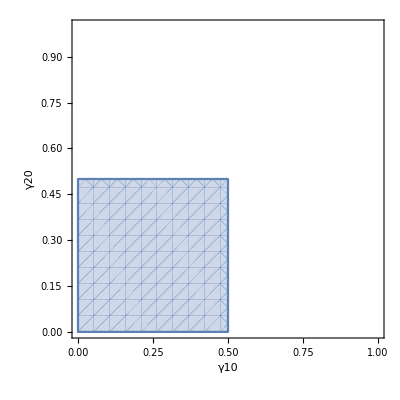

```mathematica
RegionPlot[0<=γ1b20<=1/2&&0<=γ1b10<=1/2,{γ1b10,0,1},{γ1b20,0,1},AxesLabel->{"γ10","γ20"}]
```

#### (c) γ_(1,0)=0, γ_(3,i)=0 ∀i

```mathematica
Γ1c= GammaMat[γ1c];
γ1c30=0;
γ1c31=0;
γ1c32=0;
γ1c10=0;
Choi1cConn=ChoiMatrixConnecting[Γ1c];
```

```mathematica
ei1c=Simplify[Eigenvalues[Choi1cConn]]
Reduce[CheckEigenvalues[Choi1cConn,ei1c],{γ1c21,γ1c20}]
```

{0,0,0,0,0,0,0,0,1,(-1+2 γ1c20+2 γ1c21)/(-1+γ1c20+γ1c21),(-1+γ1c20)/(-1+γ1c20+γ1c21),(-1+γ1c21)/(-1+γ1c20+γ1c21)}

True

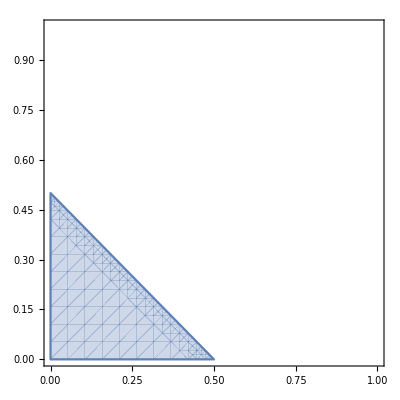

```mathematica
RegionPlot[0<=γ1c21+γ1c20<=1/2,{γ1c21,0,1},{γ1c20,0,1}]
```

#### (d) γ_(2,0)=0, γ_(3,i)=0 ∀i

This channel should always be non degradable

```mathematica
Γ1d= GammaMat[γ1d];
γ1d30=0;
γ1d31=0;
γ1d32=0;
γ1d20=0;
Choi1dConn=ChoiMatrixConnecting[Γ1d];
```

```mathematica
ei1d=Simplify[Eigenvalues[Choi1dConn]]
Reduce[CheckEigenvalues[Choi1dConn,ei1d],{γ1d21,γ1d10}]
```

{0,0,0,0,0,0,1,-(γ1d10 γ1d21)/((-1+γ1d10) (-1+γ1d21)),((-1+2 γ1d10) γ1d21)/((-1+γ1d10) (-1+γ1d21))+1/Sign[1-γ1d21],1/(1-γ1d10),1/2 ((1+γ1d10 (-2+γ1d21))/((-1+γ1d10) (-1+γ1d21))-(√((-1+γ1d10) (-1+γ1d21) (1+γ1d10 (-4+6 γ1d21-4 γ1d21^2)+γ1d10^2 (4-8 γ1d21+5 γ1d21^2)) Sign[1-γ1d21]^2))/((1-γ1d10)^(3/2) (1-γ1d21)^(3/2) Sign[1-γ1d21])),1/2 ((1+γ1d10 (-2+γ1d21))/((-1+γ1d10) (-1+γ1d21))+(√((-1+γ1d10) (-1+γ1d21) (1+γ1d10 (-4+6 γ1d21-4 γ1d21^2)+γ1d10^2 (4-8 γ1d21+5 γ1d21^2)) Sign[1-γ1d21]^2))/((1-γ1d10)^(3/2) (1-γ1d21)^(3/2) Sign[1-γ1d21]))}

True

```mathematica
Assuming[{0<=γ1d21<=1&&0<=γ1d10<=1},Simplify[Reduce[ei1d[[8]]>=0]]]
```

(γ1d21==0&&γ1d10<1)||(0<γ1d21<1&&γ1d10≤0)

### (2) γ_(1,0)=0, γ_(3,2)=0, γ_(2,1)=0

#### (a) γ_(3,0)=0

```mathematica
Γ2a= GammaMat[γ2a];
γ2a30=0;
γ2a21=0;
γ2a32=0;
γ2a10=0;
Choi2aConn=ChoiMatrixConnecting[Γ2a];
```

```mathematica
ei2a=Simplify[Eigenvalues[Choi2aConn]]
Reduce[CheckEigenvalues[Choi2aConn,ei2a],{γ2a20,γ2a31}]
```

{0,0,0,0,0,0,0,0,(-1+2 γ2a20)/(-1+γ2a20),(-1+2 γ2a31)/(-1+γ2a31),1/(1-γ2a20),1/(1-γ2a31)}

True

#### General case

```mathematica
Γ2= GammaMat[γ];
γ32=0;
γ10=0;
Choi2Conn=ChoiMatrixConnecting[Γ2];
```

```mathematica
ei2=Simplify[Eigenvalues[Choi2Conn]]
Reduce[CheckEigenvalues[Choi2Conn,ei2],{γ20,γ21,γ31,γ30}]
γ//ClearAmplitudes
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(-1+2 γ20+2 γ21)/(-1+γ20+γ21),(1+γ20 (-1+γ30)-γ30-γ21 γ31)/((-1+γ20+γ21) (-1+γ30+γ31)),(1-γ20 γ30+γ21 (-1+γ31)-γ31)/((-1+γ20+γ21) (-1+γ30+γ31)),(γ30+γ31-√((-1+γ30+γ31)^2))/(-1+γ30+γ31)}

True

```mathematica
RegionPlot3D[(0<=γ20<=1/2&&0<=γ31+γ30<=1/2),{γ20,0,1},{γ31,0,1},{γ30,0,1},AxesLabel->Automatic]
```

```mathematica
RegionPlot3D[(0<=γ20<=1/2&&0<=γ31+γ30<=1/2),{γ20,0,1},{γ31,0,1},{γ30,0,1},AxesLabel->Automatic]
```

-Graphics3D-

```mathematica
Ω=GammaMat[ω];
ρD=BuildDensityDiagonal[p];
ω31=0;
ω20=0;
ω21=0;
KrausSet2=KrausList[Ω];
MAD2=Kraus[KrausSet2];
Simplify[MAD2[ρA]]//MatrixForm
Simplify[ComplMAD[ρA,Ω]]//MatrixForm
Assuming[ω30==0,Simplify[MAD2[ρD]]//MatrixForm]
Assuming[ω30==0,Simplify[ComplMAD[ρD,Ω]]//MatrixForm]
```

(ρ00+ρ11 ω10+ρ33 ω30 | ρ01 √(1-ω10) | ρ02 | ρ03 √(1-ω30-ω32)
√(1-ω10) Conjugate[ρ01] | ρ11-ρ11 ω10 | ρ12 √(1-ω10) | ρ13 √(1-ω10) √(1-ω30-ω32)
Conjugate[ρ02] | √(1-ω10) Conjugate[ρ12] | ρ22+ρ33 ω32 | ρ23 √(1-ω30-ω32)
√(1-ω30-ω32) Conjugate[ρ03] | √(1-ω10) √(1-ω30-ω32) Conjugate[ρ13] | √(1-ω30-ω32) Conjugate[ρ23] | -ρ33 (-1+ω30+ω32))

(ρ00+ρ11+ρ22+ρ33-ρ11 ω10-ρ33 ω30-ρ33 ω32 | ρ01 √ω10 | ρ03 √ω30 | ρ23 √ω32
√ω10 Conjugate[ρ01] | ρ11 ω10 | ρ13 √ω10 √ω30 | 0
√ω30 Conjugate[ρ03] | √ω10 √ω30 Conjugate[ρ13] | ρ33 ω30 | 0
√ω32 Conjugate[ρ23] | 0 | 0 | ρ33 ω32)

(p0+p1 ω10 | 0 | 0 | 0
0 | p1-p1 ω10 | 0 | 0
0 | 0 | p2-(-1+p0+p1) ω32-p2 ω32 | 0
0 | 0 | 0 | (-1+p0+p1+p2) (-1+ω32))

(1+(-1+p0+p2) ω32+p1 (-ω10+ω32) | 0 | 0 | 0
0 | p1 ω10 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | -((-1+p0+p1+p2) ω32))

### (3) Only γ_(3,i)!=0 ∀i

```mathematica
Γ3= GammaMat[γ3];
γ321=0;
γ320=0;
γ310=0;
Choi3Conn=ChoiMatrixConnecting[Γ3];
```

```mathematica
ei3=Simplify[Eigenvalues[Choi3Conn]]
Reduce[CheckEigenvalues[Choi3Conn,ei3],{γ330,γ331,γ332}]
```

{0,0,0,0,0,0,0,0,0,0,0,0,(-1+2 γ330+2 γ331+2 γ332)/(-1+γ330+γ331+γ332),(-1+γ330+γ331)/(-1+γ330+γ331+γ332),(-1+γ330+γ332)/(-1+γ330+γ331+γ332),(-1+γ331+γ332)/(-1+γ330+γ331+γ332)}

True

```mathematica
RegionPlot3D[(γ30+γ31+γ32<=1/2),{γ30,0,1},{γ31,0,1},{γ32,0,1},AxesLabel->Automatic]
```

-Graphics3D-

### (4) γ_(1,0)=0,γ_(3,2)=0, γ_(2,0)=0

Equivalent to (2)

### (5) γ_(1,0)=0,γ_(3,2)=0, γ_(3,1)=0

Equivalent to (2)

### (6) Only γ_(i,0)!=0 ∀i

```mathematica
Γ6= GammaMat[γ6];
γ621=0;
γ632=0;
γ631=0;
Choi6Conn=ChoiMatrixConnecting[Γ6];
```

```mathematica
ei6=Simplify[Eigenvalues[Choi6Conn]]
Reduce[CheckEigenvalues[Choi6Conn,ei6],{γ630,γ620,γ610}]
```

{0,0,0,0,0,0,0,0,0,0,0,0,(-1+2 γ610)/(-1+γ610),(-1+2 γ620)/(-1+γ620),(-1+2 γ630)/(-1+γ630),(-1+γ620 γ630+γ610 (γ620+γ630-2 γ620 γ630))/((-1+γ610) (-1+γ620) (-1+γ630))}

True

```mathematica
RegionPlot3D[(0<=γ10<=1/2&&0<=γ20<=1/2&&0<=γ30<=1/2),{γ10,0,1},{γ20,0,1},{γ30,0,1},AxesLabel->Automatic]
```

-Graphics3D-

### (7)γ_(1,0)=0,γ_(2,0)=0, γ_(3,1)=0

```mathematica
Γ7= GammaMat[γ7];
γ720=0;
γ710=0;
γ731=0;
Choi7Conn=ChoiMatrixConnecting[Γ7];
```

```mathematica
ei7=Simplify[Eigenvalues[Choi7Conn]]
Reduce[CheckEigenvalues[Choi7Conn,ei7],{γ721,γ732,γ730}]
```

{0,0,0,0,0,0,0,0,0,0,-(γ721 γ732)/((-1+γ721) (-1+γ730+γ732)),(1-2 γ730-2 γ732+γ721 (-1+2 γ730+3 γ732))/((-1+γ721) (-1+γ730+γ732)),1/(1-γ721),(-1+γ732)/(-1+γ730+γ732),1/2 (1/((-1+γ721) (-1+γ730+γ732))-γ730/((-1+γ721) (-1+γ730+γ732))+(γ721 (-2+2 γ730+γ732))/((-1+γ721) (-1+γ730+γ732))-(√((-1+γ721) (-1+γ730+γ732) ((-1+γ730)^2+γ721^2 (4+4 γ730^2+8 γ730 (-1+γ732)-8 γ732+5 γ732^2)-2 γ721 (2+2 γ730^2-3 γ732+2 γ732^2+γ730 (-4+3 γ732)))))/((1-γ721)^(3/2) (1-γ732)^(3/2) ((-1+γ730+γ732)/(-1+γ732))^(3/2))),1/2 (1/((-1+γ721) (-1+γ730+γ732))-γ730/((-1+γ721) (-1+γ730+γ732))+(γ721 (-2+2 γ730+γ732))/((-1+γ721) (-1+γ730+γ732))+(√((-1+γ721) (-1+γ730+γ732) ((-1+γ730)^2+γ721^2 (4+4 γ730^2+8 γ730 (-1+γ732)-8 γ732+5 γ732^2)-2 γ721 (2+2 γ730^2-3 γ732+2 γ732^2+γ730 (-4+3 γ732)))))/((1-γ721)^(3/2) (1-γ732)^(3/2) ((-1+γ730+γ732)/(-1+γ732))^(3/2)))}

True

```mathematica
Assuming[{0<=γ721<=1&&0<=γ732<=1&&0<=γ730<=1&&0<=γ732+γ730<=1},Simplify[Reduce[ei7[[11]]>0]]]
Assuming[{0<=γ721<=1&&0<=γ732<=1&&0<=γ730<=1&&0<=γ732+γ730<=1},Simplify[Reduce[ei7[[11]]==0]]]
```

False

(γ721==0&&γ730+γ732≠1)||(γ732==0&&1+γ721 γ730≠γ721+γ730)

### (8)γ_(3,2)=0,γ_(2,0)=0, γ_(2,1)=0

Equivalent to (2)

### (9) γ_(3,2)=0,γ_(2,0)=0, γ_(3,1)=0

```mathematica
Γ9= GammaMat[γ9];
γ920=0;
γ932=0;
γ931=0;
Choi9Conn=ChoiMatrixConnecting[Γ9];
```

```mathematica
ei9=Simplify[Eigenvalues[Choi9Conn]]
Reduce[CheckEigenvalues[Choi9Conn,ei9],{γ910,γ930,γ921}]
```

{0,0,0,0,0,0,0,0,0,0,-(γ910 γ921)/((-1+γ910) (-1+γ921)),(1-2 γ921+γ910 (-1+3 γ921))/((-1+γ910) (-1+γ921)),(-1+2 γ930)/(-1+γ930),(1-γ910 γ930)/((-1+γ910) (-1+γ930)),1/(2 (1-γ910)^(3/2) (-1+γ921)^2 (1-γ930)^(3/2))(√(1-γ910) √(1-γ930)-√(1-γ910) γ921 (1-γ930)^(3/2)-√(1-γ910) γ910 (2-3 γ921+γ921^2) (1-γ930)^(3/2)+√(1-γ921) √(-((-1+γ910) (-1+γ921) (1+γ910 (-4+6 γ921-4 γ921^2)+γ910^2 (4-8 γ921+5 γ921^2)) (-1+γ930)^3))-√(1-γ910) √(1-γ930) γ930),1/(2 (1-γ910)^(3/2) (-1+γ921)^2 (1-γ930)^(3/2))(√(1-γ910) √(1-γ930)-√(1-γ910) γ921 (1-γ930)^(3/2)-√(1-γ910) γ910 (2-3 γ921+γ921^2) (1-γ930)^(3/2)-√(1-γ921) √(-((-1+γ910) (-1+γ921) (1+γ910 (-4+6 γ921-4 γ921^2)+γ910^2 (4-8 γ921+5 γ921^2)) (-1+γ930)^3))-√(1-γ910) √(1-γ930) γ930)}

$Aborted

```mathematica
Assuming[{0<=γ910<=1&&0<=γ930<=1&&0<=γ921<=1},Simplify[Reduce[ei9[[11]]>0]]]
Assuming[{0<=γ910<=1&&0<=γ930<=1&&0<=γ921<=1},Simplify[Reduce[ei9[[11]]==0]]]
```

False

(γ910==0&&γ921≠1)||(γ921==0&&γ910≠1)

### (10) γ_(3,0)=0,γ_(2,1)=0, γ_(1,0)=0

Equivalent to (7)

### (11) γ_(3,0)=0 ,γ_(3,2)=0, γ_(1,0)=0

Equivalent to (2)

### (12) γ_(3,0)=0 ,γ_(3,2)=0, γ_(2,1)=0

Equivalent to (9)

### (13) γ_(3,0)=0 ,γ_(2,0)=0, γ_(2,1)=0

Equivalent to (7)

### (14)γ_(3,0)=0 ,γ_(2,0)=0, γ_(3,2)=0

```mathematica
Γ14= GammaMat[γ14];
γ1420=0;
γ1432=0;
γ1430=0;
Choi14Conn=ChoiMatrixConnecting[Γ14];
```

```mathematica
ei14=Simplify[Eigenvalues[Choi14Conn]]
Reduce[CheckEigenvalues[Choi14Conn,ei14],{γ1410,γ1431,γ1421}]
```

{0,0,0,0,0,0,0,0,0,-(γ1410 γ1421)/((-1+γ1410) (-1+γ1421)),(1-2 γ1421+γ1410 (-1+3 γ1421))/((-1+γ1410) (-1+γ1421)),-(γ1410 γ1431)/((-1+γ1410) (-1+γ1431)),(1-2 γ1431+γ1410 (-1+3 γ1431))/((-1+γ1410) (-1+γ1431)),1/(1-γ1410),-1/(2 (1-γ1410)^(3/2) (-1+γ1421)^2 (-1+γ1431)^2)(-√(1-γ1410)+√(1-γ1410) γ1421+√(1-γ1410) γ1431-√(1-γ1410) γ1421^2 γ1431-√(1-γ1410) γ1421 γ1431^2+√(1-γ1410) γ1421^2 γ1431^2-√(1-γ1410) γ1410 (-1+γ1421) (-1+γ1431) (-2+γ1421+γ1431)-√(-((-1+γ1410) (-1+γ1421)^2 (-1+γ1431)^2 ((-1+γ1421 γ1431)^2-2 γ1410 (2-3 γ1431+2 γ1431^2+γ1421 (-3+6 γ1431-5 γ1431^2)+γ1421^2 (2-5 γ1431+4 γ1431^2))+γ1410^2 (4-8 γ1431+5 γ1431^2-2 γ1421 (4-9 γ1431+6 γ1431^2)+γ1421^2 (5-12 γ1431+8 γ1431^2)))))),-1/(2 (1-γ1410)^(3/2) (-1+γ1421)^2 (-1+γ1431)^2)(-√(1-γ1410)+√(1-γ1410) γ1421+√(1-γ1410) γ1431-√(1-γ1410) γ1421^2 γ1431-√(1-γ1410) γ1421 γ1431^2+√(1-γ1410) γ1421^2 γ1431^2-√(1-γ1410) γ1410 (-1+γ1421) (-1+γ1431) (-2+γ1421+γ1431)+√(-((-1+γ1410) (-1+γ1421)^2 (-1+γ1431)^2 ((-1+γ1421 γ1431)^2-2 γ1410 (2-3 γ1431+2 γ1431^2+γ1421 (-3+6 γ1431-5 γ1431^2)+γ1421^2 (2-5 γ1431+4 γ1431^2))+γ1410^2 (4-8 γ1431+5 γ1431^2-2 γ1421 (4-9 γ1431+6 γ1431^2)+γ1421^2 (5-12 γ1431+8 γ1431^2))))))}

$Aborted

```mathematica
Assuming[{0<=γ1410<=1&&0<=γ1431<=1&&0<=γ1421<=1},Simplify[Reduce[ei14[[10]]>0]]]
Assuming[{0<=γ1410<=1&&0<=γ1431<=1&&0<=γ1421<=1},Simplify[Reduce[ei14[[10]]==0]]]
```

False

(γ1410==0&&γ1421≠1)||(γ1421==0&&γ1410≠1)

### (15)γ_(3,0)=0 ,γ_(1,0)=0, γ_(3,1)=0

```mathematica
Γ15= GammaMat[γ15];
γ1530=0;
γ1531=0;
γ1510=0;
Choi15Conn=ChoiMatrixConnecting[Γ15];
```

```mathematica
ei15=Simplify[Eigenvalues[Choi15Conn]]
Reduce[CheckEigenvalues[Choi15Conn,ei15],{γ1521,γ1520,γ1532}]
```

{0,0,0,0,0,0,0,0,0,-(γ1520 γ1532)/((-1+γ1520+γ1521) (-1+γ1532)),-(γ1521 γ1532)/((-1+γ1520+γ1521) (-1+γ1532)),(1-2 γ1532+γ1520 (-1+3 γ1532)+γ1521 (-1+3 γ1532))/((-1+γ1520+γ1521) (-1+γ1532)),(-1+γ1520)/(-1+γ1520+γ1521),(-1+γ1521)/(-1+γ1520+γ1521),-1/(2 (1-γ1521)^(3/2) ((-1+γ1520+γ1521)/(-1+γ1521))^(3/2) (-1+γ1532)^2)(-√(1-γ1521) √((-1+γ1520+γ1521)/(-1+γ1521))+√(1-γ1521) √((-1+γ1520+γ1521)/(-1+γ1521)) γ1532+γ1520 √(1-γ1521) √((-1+γ1520+γ1521)/(-1+γ1521)) (2-3 γ1532+γ1532^2)+√(1-γ1521) γ1521 √((-1+γ1520+γ1521)/(-1+γ1521)) (2-3 γ1532+γ1532^2)+√(1-γ1532) √((-1+γ1520+γ1521) (-1+γ1532) (1+γ1521 (-4+6 γ1532-4 γ1532^2)+γ1520^2 (4-8 γ1532+5 γ1532^2)+γ1521^2 (4-8 γ1532+5 γ1532^2)+2 γ1520 (-2+3 γ1532-2 γ1532^2+γ1521 (4-8 γ1532+5 γ1532^2))))),-1/(2 (1-γ1521)^(3/2) ((-1+γ1520+γ1521)/(-1+γ1521))^(3/2) (-1+γ1532)^2)(-√(1-γ1521) √((-1+γ1520+γ1521)/(-1+γ1521))+√(1-γ1521) √((-1+γ1520+γ1521)/(-1+γ1521)) γ1532+γ1520 √(1-γ1521) √((-1+γ1520+γ1521)/(-1+γ1521)) (2-3 γ1532+γ1532^2)+√(1-γ1521) γ1521 √((-1+γ1520+γ1521)/(-1+γ1521)) (2-3 γ1532+γ1532^2)-√(1-γ1532) √((-1+γ1520+γ1521) (-1+γ1532) (1+γ1521 (-4+6 γ1532-4 γ1532^2)+γ1520^2 (4-8 γ1532+5 γ1532^2)+γ1521^2 (4-8 γ1532+5 γ1532^2)+2 γ1520 (-2+3 γ1532-2 γ1532^2+γ1521 (4-8 γ1532+5 γ1532^2)))))}

$Aborted

```mathematica
Assuming[{0<=γ1532<=1&&0<=γ1520<=1&&0<=γ1521<=1&&0<=γ1520+γ1521<=1},Simplify[Reduce[ei15[[10]]>0]]]
Assuming[{0<=γ1532<=1&&0<=γ1520<=1&&0<=γ1521<=1&&0<=γ1520+γ1521<=1},Simplify[Reduce[ei15[[10]]==0]]]
```

False

(γ1520==0&&1+γ1521 γ1532≠γ1521+γ1532)||(γ1532==0&&γ1520+γ1521≠1)

### (16) γ_(3,0)=0 ,γ_(2,1)=0, γ_(3,1)=0

Equivalent to (9)

### (17) γ_(3,0)=0 ,γ_(2,0)=0, γ_(3,1)=0

```mathematica
Γ17= GammaMat[γ17];
γ1720=0;
γ1731=0;
γ1730=0;
Choi17Conn=ChoiMatrixConnecting[Γ17];
```

```mathematica
ei17=Simplify[Eigenvalues[Choi17Conn]]
```

{0,0,0,0,0,0,0,-(γ1710 γ1721)/((-1+γ1710) (-1+γ1721)),-(γ1721 γ1732)/((-1+γ1721) (-1+γ1732)),-(γ1710 γ1721 γ1732)/((-1+γ1710) (-1+γ1721) (-1+γ1732)),(-1+γ1710+γ1721+2 γ1732-2 γ1710 γ1732-3 γ1721 γ1732+γ1710 γ1721 (-1+4 γ1732))/((-1+γ1710) (-1+γ1721) (-1+γ1732)),1/(1-γ1710),1/(2 (1-γ1710)^(3/2) (-1+γ1721)^2 (1-γ1732)^(3/2))(√(1-γ1710) √(1-γ1732)-√(1-γ1710) γ1721 (1-γ1732)^(3/2)-√(1-γ1710) γ1710 (2-3 γ1721+γ1721^2) (1-γ1732)^(3/2)+√(1-γ1721) √(-((-1+γ1710) (-1+γ1721) (1+γ1710 (-4+6 γ1721-4 γ1721^2)+γ1710^2 (4-8 γ1721+5 γ1721^2)) (-1+γ1732)^3))-√(1-γ1710) √(1-γ1732) γ1732),1/(2 (1-γ1710)^(3/2) (-1+γ1721)^2 (1-γ1732)^(3/2))(√(1-γ1710) √(1-γ1732)-√(1-γ1710) γ1721 (1-γ1732)^(3/2)-√(1-γ1710) γ1710 (2-3 γ1721+γ1721^2) (1-γ1732)^(3/2)-√(1-γ1721) √(-((-1+γ1710) (-1+γ1721) (1+γ1710 (-4+6 γ1721-4 γ1721^2)+γ1710^2 (4-8 γ1721+5 γ1721^2)) (-1+γ1732)^3))-√(1-γ1710) √(1-γ1732) γ1732),1/(2 (1-γ1710)^(3/2) (1-γ1721)^(3/2) (-1+γ1732)^2)(√(1-γ1710) √(1-γ1721)-√(1-γ1710) √(1-γ1721) γ1732-√(1-γ1710) √(1-γ1721) γ1721 (2-3 γ1732+γ1732^2)+√(1-γ1710) γ1710 √(1-γ1721) (-1+γ1732) (1+γ1721 (-3+2 γ1732))+√(1-γ1732) √(-((-1+γ1710) (-1+γ1721) (-1+γ1732) (1+γ1721 (-4+6 γ1732-4 γ1732^2)+γ1721^2 (4-8 γ1732+5 γ1732^2)-2 γ1710 (1+γ1721 (-5+9 γ1732-6 γ1732^2)+γ1721^2 (6-13 γ1732+8 γ1732^2))+γ1710^2 (1-2 γ1721 (3-6 γ1732+4 γ1732^2)+γ1721^2 (9-20 γ1732+12 γ1732^2)))))),1/(2 (1-γ1710)^(3/2) (1-γ1721)^(3/2) (-1+γ1732)^2)(√(1-γ1710) √(1-γ1721)-√(1-γ1710) √(1-γ1721) γ1732-√(1-γ1710) √(1-γ1721) γ1721 (2-3 γ1732+γ1732^2)+√(1-γ1710) γ1710 √(1-γ1721) (-1+γ1732) (1+γ1721 (-3+2 γ1732))-√(1-γ1732) √(-((-1+γ1710) (-1+γ1721) (-1+γ1732) (1+γ1721 (-4+6 γ1732-4 γ1732^2)+γ1721^2 (4-8 γ1732+5 γ1732^2)-2 γ1710 (1+γ1721 (-5+9 γ1732-6 γ1732^2)+γ1721^2 (6-13 γ1732+8 γ1732^2))+γ1710^2 (1-2 γ1721 (3-6 γ1732+4 γ1732^2)+γ1721^2 (9-20 γ1732+12 γ1732^2))))))}

```mathematica
ChoiConn=ChoiMatrixConnecting[Γgen];
ChoiConn=Replace[#,ConstantArray[0,Length@#[[1]]]->Sequence[],{1}]&@ChoiConn;
ChoiConn=Replace[#,ConstantArray[0,Length@#[[1]]]->Sequence[],{1}]&@Transpose[ChoiConn];
ChoiConn//MatrixForm
```

(1 | 0 | (√γ10)/(√(1-γ10)) | 0 | 0 | (√γ20)/(√(1+γ20/(-1+γ21)) √(1-γ21)) | 0 | 0 | 0 | 0 | 0 | (√γ30)/(√(1+γ31/(-1+γ32)) √(1-γ32) √(1+γ30/(-1+γ31+γ32))) | 0 | 0
0 | 2+1/(-1+γ10) | 0 | 0 | 0 | 0 | (√γ21)/(√(1+γ20/(-1+γ21)) √(1-γ21)) | 0 | 0 | 0 | 0 | 0 | (√γ31)/(√(1+γ31/(-1+γ32)) √(1-γ32) √(1+γ30/(-1+γ31+γ32))) | 0
(√γ10)/(√(1-γ10)) | 0 | γ10/(1-γ10) | 0 | 0 | (√γ10 √γ20)/(√(1-γ10) √(1+γ20/(-1+γ21)) √(1-γ21)) | 0 | 0 | 0 | 0 | 0 | (√γ10 √γ30)/(√(1-γ10) √(1+γ31/(-1+γ32)) √(1-γ32) √(1+γ30/(-1+γ31+γ32))) | 0 | 0
0 | 0 | 0 | ((-1+γ10) (-1+2 γ20)+(-2+3 γ10) γ21)/((-1+γ10) (-1+γ20+γ21)) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (√(1-γ20-γ21) √γ32)/(√(1+γ20/(-1+γ21)) √(1-γ21) √(1+γ31/(-1+γ32)) √(1-γ32) √(1+γ30/(-1+γ31+γ32)))
0 | 0 | 0 | 0 | -(γ10 γ21)/((-1+γ10) (-1+γ20+γ21)) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
(√γ20)/(√(1+γ20/(-1+γ21)) √(1-γ21)) | 0 | (√γ10 √γ20)/(√(1-γ10) √(1+γ20/(-1+γ21)) √(1-γ21)) | 0 | 0 | -γ20/(-1+γ20+γ21) | 0 | 0 | 0 | 0 | 0 | (√γ20 √γ30)/(√(1+γ20/(-1+γ21)) √(1-γ21) √(1+γ31/(-1+γ32)) √(1-γ32) √(1+γ30/(-1+γ31+γ32))) | 0 | 0
0 | (√γ21)/(√(1+γ20/(-1+γ21)) √(1-γ21)) | 0 | 0 | 0 | 0 | -γ21/(-1+γ20+γ21) | 0 | 0 | 0 | 0 | 0 | (√γ21 √γ31)/(√(1+γ20/(-1+γ21)) √(1-γ21) √(1+γ31/(-1+γ32)) √(1-γ32) √(1+γ30/(-1+γ31+γ32))) | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | ((-1+γ20+γ21) ((-1+γ10) (-1+2 γ30)+(-2+3 γ10) γ31)+((-1+γ10) (-2+3 γ20)+(-3+4 γ10) γ21) γ32)/((-1+γ10) (-1+γ20+γ21) (-1+γ30+γ31+γ32)) | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(γ10 ((-1+γ20+γ21) γ31+γ21 γ32))/((-1+γ10) (-1+γ20+γ21) (-1+γ30+γ31+γ32)) | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(γ20 γ32)/((-1+γ20+γ21) (-1+γ30+γ31+γ32)) | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(γ21 γ32)/((-1+γ20+γ21) (-1+γ30+γ31+γ32)) | 0 | 0 | 0
(√γ30)/(√(1+γ31/(-1+γ32)) √(1-γ32) √(1+γ30/(-1+γ31+γ32))) | 0 | (√γ10 √γ30)/(√(1-γ10) √(1+γ31/(-1+γ32)) √(1-γ32) √(1+γ30/(-1+γ31+γ32))) | 0 | 0 | (√γ20 √γ30)/(√(1+γ20/(-1+γ21)) √(1-γ21) √(1+γ31/(-1+γ32)) √(1-γ32) √(1+γ30/(-1+γ31+γ32))) | 0 | 0 | 0 | 0 | 0 | -γ30/(-1+γ30+γ31+γ32) | 0 | 0
0 | (√γ31)/(√(1+γ31/(-1+γ32)) √(1-γ32) √(1+γ30/(-1+γ31+γ32))) | 0 | 0 | 0 | 0 | (√γ21 √γ31)/(√(1+γ20/(-1+γ21)) √(1-γ21) √(1+γ31/(-1+γ32)) √(1-γ32) √(1+γ30/(-1+γ31+γ32))) | 0 | 0 | 0 | 0 | 0 | -γ31/(-1+γ30+γ31+γ32) | 0
0 | 0 | 0 | (√(1-γ20-γ21) √γ32)/(√(1+γ20/(-1+γ21)) √(1-γ21) √(1+γ31/(-1+γ32)) √(1-γ32) √(1+γ30/(-1+γ31+γ32))) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -γ32/(-1+γ30+γ31+γ32))

```mathematica
Eigenvalues[ChoiConn]
```

$Aborted

### Check degradability of channel obtained from complete damping of levels 1 and 2

```mathematica
ρA=BuildDensity[ρ];
γ//ClearAmplitudes
Γ=GammaMat[γ];

γ10=1;
γ21=1-γ20;

KrausCD21={{{1,0,0,0},{0,1,0,0},{0,0,0,0},{0,0,0,Sqrt[1-γ30-γ31-γ32]}},{{0,0,0,Sqrt[γ30]},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,Sqrt[γ31]},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,Sqrt[γ32]},{0,0,0,0}}};

ch3//Clear

ch3=Kraus[KrausCD21];

InverseNotKraus30={{{1,0,0,0},{0,1,0,0},{0,0,0,0},{0,0,0,(1-γ30/(1-γ31-γ32))^(-1/2)}},{{0,0,0,Sqrt[γ30/(1-γ30-γ31-γ32)]},{0,0,0,0},{0,0,0,0},{0,0,0,0}}};
InverseNotKraus31={{{1,0,0,0},{0,1,0,0},{0,0,0,0},{0,0,0,(1-γ31/(1-γ32))^(-1/2)}},{{0,0,0,Sqrt[γ31/(1-γ31-γ32)]},{0,0,0,0},{0,0,0,0},{0,0,0,0}}};
InverseNotKraus32={{{1,0,0,0},{0,1,0,0},{0,0,0,0},{0,0,0,(1-γ32)^(-1/2)}},{{0,0,0,Sqrt[γ32/(1-γ32)]},{0,0,0,0},{0,0,0,0},{0,0,0,0}}};

InverseNotKraus3={InverseNotKraus30,InverseNotKraus31,InverseNotKraus32};

InverseNotKraus30[[0]].ρA.ConjugateTranspose[InverseNotKraus30[[0]]]-InverseNotKraus30[[1]].ρA.ConjugateTranspose[InverseNotKraus30[[1]]];

InverseADC3[θ_,i_]:=Part[InverseNotKraus3,i][[1]].θ.ConjugateTranspose[Part[InverseNotKraus3,i][[1]]]- Part[InverseNotKraus3,i][[2]].θ.ConjugateTranspose[Part[InverseNotKraus3,i][[2]]];

InverseMAD3[den_]:=(
den1=den;
Do[
InverseADC3[den,i],
{i,1,3}
];
den1//Simplify
);

ch3[InverseMAD3[ρA]]//MatrixForm
```

(ρ00+γ30 ρ33 | ρ01 | 0 | √(1-γ30-γ31-γ32) ρ03
Conjugate[ρ01] | ρ11+γ31 ρ33 | 0 | √(1-γ30-γ31-γ32) ρ13
0 | 0 | γ32 ρ33 | 0
√(1-γ30-γ31-γ32) Conjugate[ρ03] | √(1-γ30-γ31-γ32) Conjugate[ρ13] | 0 | (1-γ30-γ31-γ32) ρ33)

## 4 decay MAD4 deg conditions

```mathematica
γ//ClearAmplitudes
```

```mathematica
γ10=0;
γ32=0;
γ21=γ4;
γ20=γ1;
γ30=γ2;
γ31=γ3;
```

```mathematica
choi4=ChoiMatrixConnecting[GammaMat[γ]];
```

```mathematica
choi4//Eigenvalues//Simplify
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(-1+2 γ2+2 γ3)/(-1+γ2+γ3),(-1+2 γ1+2 γ4)/(-1+γ1+γ4),(1+γ1 (-1+γ2)-γ2-γ3 γ4)/((-1+γ2+γ3) (-1+γ1+γ4)),(-γ1 γ2+(-1+γ3) (-1+γ4))/((-1+γ2+γ3) (-1+γ1+γ4))}

```mathematica
MAD[γ][BuildDensity[ρ]]//MatrixForm
ComplMAD[BuildDensity[ρ],GammaMat[γ]]//MatrixForm
```

(ρ00+γ1 ρ22+γ2 ρ33 | ρ01 | √(1-γ1-γ4) ρ02 | √(1-γ2-γ3) ρ03
Conjugate[ρ01] | ρ11+γ4 ρ22+γ3 ρ33 | √(1-γ1-γ4) ρ12 | √(1-γ2-γ3) ρ13
√(1-γ1-γ4) Conjugate[ρ02] | √(1-γ1-γ4) Conjugate[ρ12] | (1-γ1-γ4) ρ22 | √(1-γ2-γ3) √(1-γ1-γ4) ρ23
√(1-γ2-γ3) Conjugate[ρ03] | √(1-γ2-γ3) Conjugate[ρ13] | √(1-γ2-γ3) √(1-γ1-γ4) Conjugate[ρ23] | (1-γ2-γ3) ρ33)

(ρ00+ρ11+ρ22-γ1 ρ22-γ4 ρ22+ρ33-γ2 ρ33-γ3 ρ33 | √γ1 ρ02 | √γ4 ρ12 | √γ2 ρ03 | √γ3 ρ13
√γ1 Conjugate[ρ02] | γ1 ρ22 | 0 | √γ1 √γ2 ρ23 | 0
√γ4 Conjugate[ρ12] | 0 | γ4 ρ22 | 0 | √γ3 √γ4 ρ23
√γ2 Conjugate[ρ03] | √γ1 √γ2 Conjugate[ρ23] | 0 | γ2 ρ33 | 0
√γ3 Conjugate[ρ13] | 0 | √γ3 √γ4 Conjugate[ρ23] | 0 | γ3 ρ33)